```mathematica
ClearAll[GraphPartion`CompareIsoperimetricAlgs]

SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

v::shdw: Symbol v appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

k::shdw: Symbol k appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

n::shdw: Symbol n appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

e::shdw: Symbol e appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

CompareIsoperimetricAlgs::shdw: Symbol CompareIsoperimetricAlgs appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

ShowAll::shdw: Symbol ShowAll appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

Global`

```mathematica
SquareGrid[n_] := System`GridGraph[{n,n}, 
VertexLabels->If[n<5,Automatic,None],VertexWeight->Table[1/n/n,n*n], EdgeWeight->Automatic];
```

```mathematica
g= SquareGrid[3];
{ShowSpectralCut[g],ShowIsoperimetricCut[g], ShowMultipleFiedlerCut[g], ShowMultipleIsoperimetricCut[g]}
(*ShowMultipleFiedlerCut[g]*)
(*MultipleIsoperimetricVector[g];*)
```

{ShowSpectralCut[SquareGrid[3]],ShowIsoperimetricCut[SquareGrid[3]],ShowMultipleFiedlerCut[SquareGrid[3]],ShowMultipleIsoperimetricCut[SquareGrid[3]]}

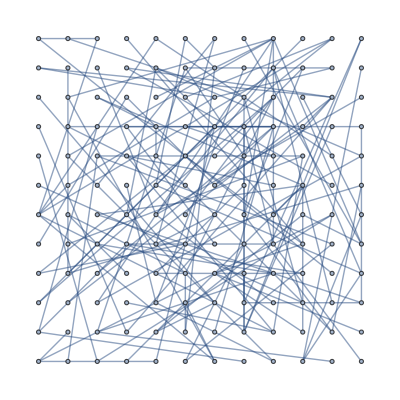

```mathematica
(*Generate grid graphs with locality by restrict the maximum distance between any pair of verices*)
RandomGrid1[m_,n_,maxDist_:1, maxFanOut_:4]:= Module[{elist={},
vlist = Range[1,m*n],
vcoords= Flatten[Table[{i,j},{i,1,m},{j,1,n}],1],
 newE, neighbor},

Vertex1D[ij_] := (First[ij]-1)*n+Last[ij];
Neighbors[i_,j_,dist_] := Select[Flatten[Table[{i+di, j+dj},{di,-dist,dist},{dj,-dist,dist}],1],
1<=First[#]≤m && 1≤Last[#]≤n && #≠{i,j}&];
elist={};
Do[AppendTo[elist,{Vertex1D[{i,j}],Vertex1D[neighbor]}],
{i,1,m},{j,1,n},{neighbor, RandomChoice[Neighbors[i,j,maxDist],(*RandomInteger[{1,*)maxFanOut(*}]*)]}]
elist =DeleteDuplicates[elist,#1==#2||#1==Reverse[#2]& ];
(*Make sure that the result graph is connected*)
With[{components=#[[1]]&/@ConnectedComponents[elist]},
If[Length[components]>1,
elist=Join[elist, Map[{components[[1]], #}&,components[[2;;]]]];,
Nothing]];
newG=System`Graph[vlist,elist,VertexCoordinates->vcoords,
System`VertexWeight->Table[1/Length[vlist], Length[vlist]],System`EdgeWeight-> Table[1,Length[elist]],
System`VertexLabels->If[Max[m,n]<5,Automatic, None],
System`EdgeStyle->Directive[Opacity[0.5], Thick](*, EdgeShapeFunction->"Arrow"*)];
newG (*UndirectedGraph[newG]*)]
g=RandomGrid1[12,12, maxDist=10, maxFanOut=1]
```

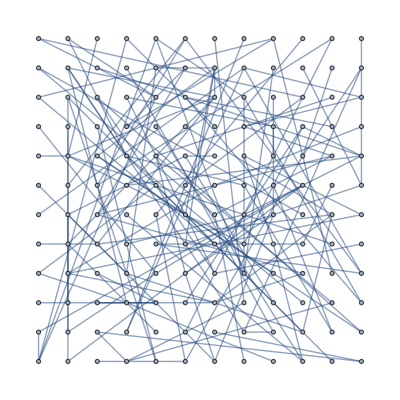
```mathematica
-Graphics-
System`RandomGraph[{50,100},5]
```

-Graphics-

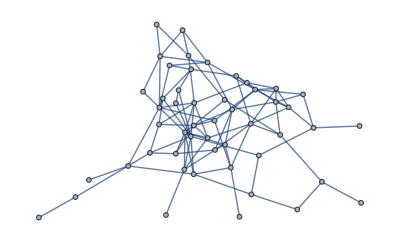
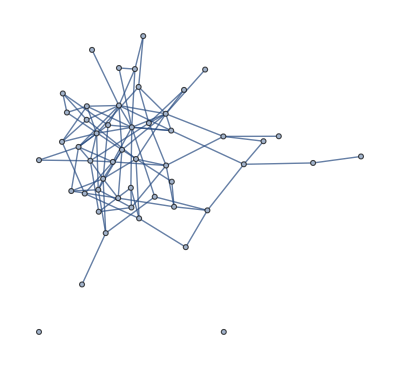
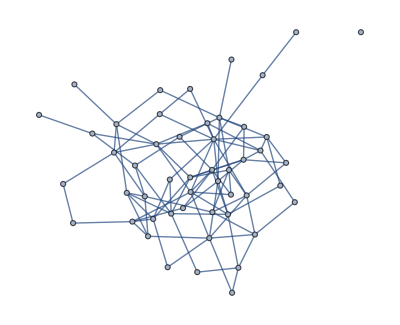
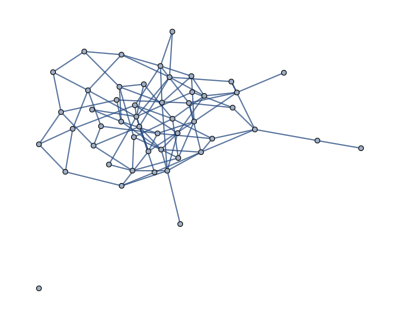
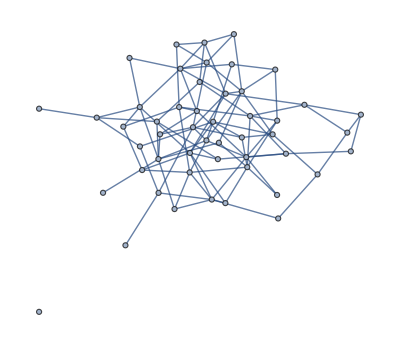

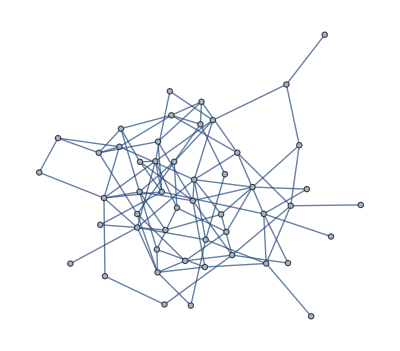
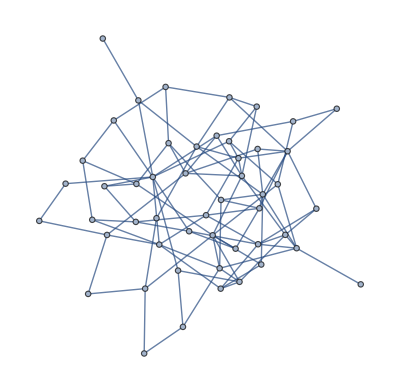
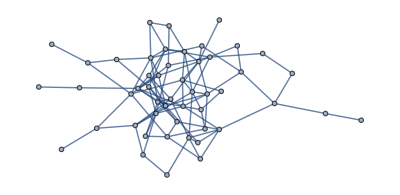

```mathematica
Select[System`RandomGraph[{50,100},5],ConnectedGraphQ]
```

### Random Graphs

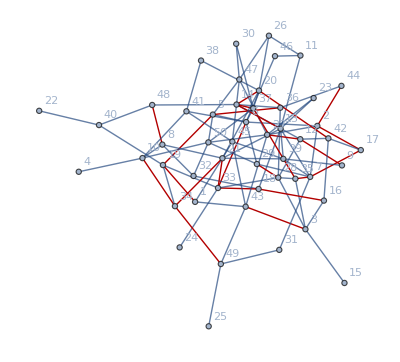
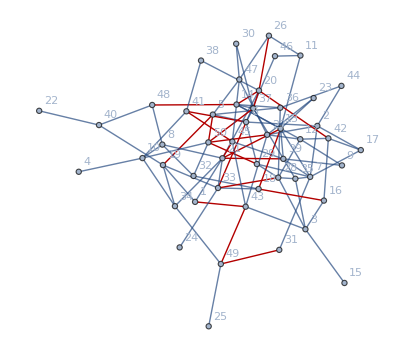
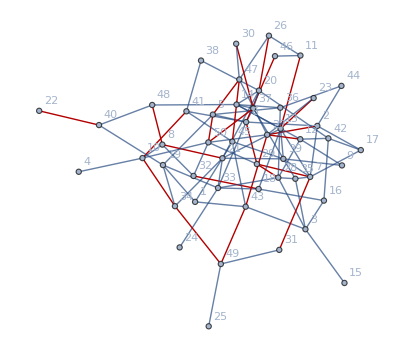
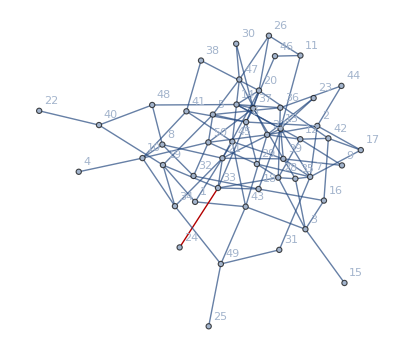
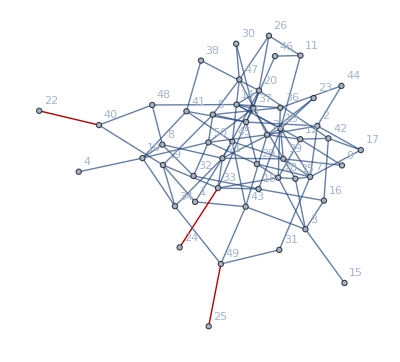
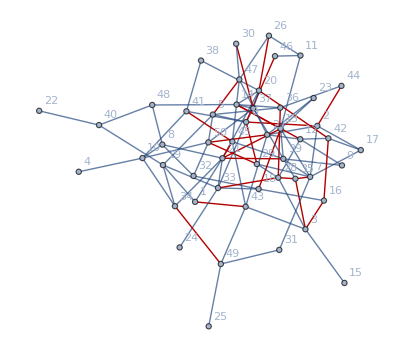
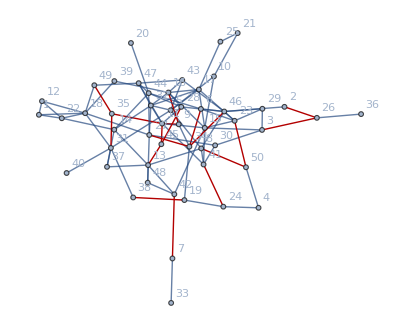
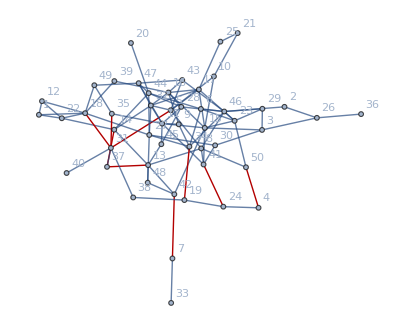
ground | Isoperimetric |  | MultipleIsoperimetric | 
11 | -Graphics- | 104.167 | -Graphics- | 91.6667
32 | -Graphics- | 106.952 |  | 
38 | -Graphics- | 51.0204 |  | 
12 | -Graphics- | 53.1915 |  | 
2 | -Graphics- | 104.167 |  | 
27 | -Graphics- | 98.6842 | -Graphics- | 60.9756
26 | -Graphics- | 51.0204 |  | 
38 | -Graphics- | 114.286 |  | 
23 | -Graphics- | 114.601 |  | 
49 | -Graphics- | 51.0204 |  |

```mathematica
v = 50; e=100; k = 5;  (*k is the number of basis vector to use*)
spanners = Select[System`RandomGraph[{v,e},2],ConnectedGraphQ];
spanners =UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/v,v], EdgeWeight->Automatic]&/@spanners;

grid = Flatten[Map[(CompareIsoperimetricAlgs[#, k, ShowAll->True] &), spanners], 1]; 
Grid[Prepend[grid, {"ground", "Isoperimetric", Null, "MultipleIsoperimetric" , Null}], Alignment -> Center, Frame -> All]
```

#### Asymmetric vs. Symmetric

Eigenvalues::arh: Because finding 144 out of the 144 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

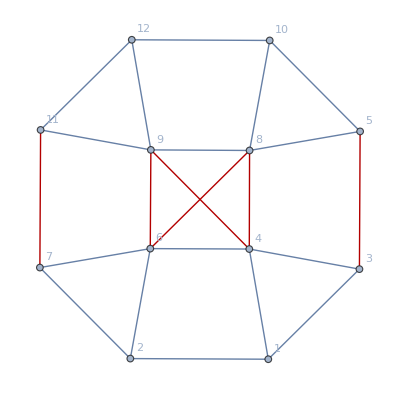
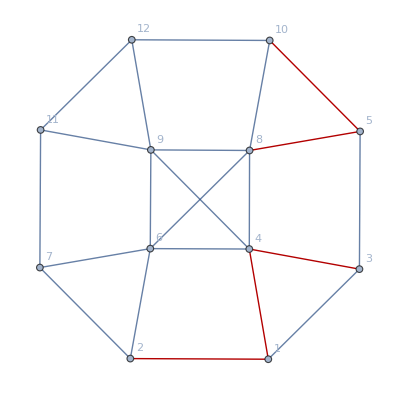
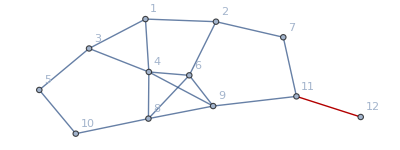
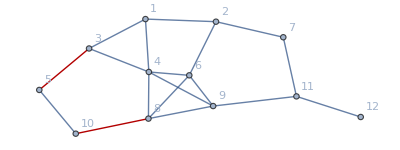
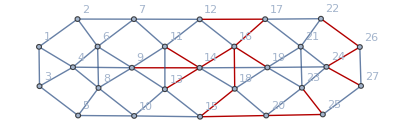
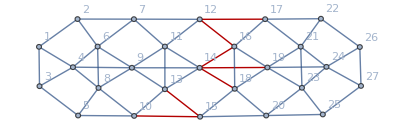
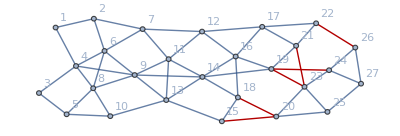
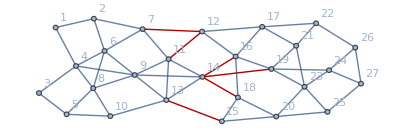
ground | Isoperimetric |  | MultipleIsoperimetric | AvgScore
-Graphics- | 24. | -Graphics- | 26.6667 | -0.0372247
-Graphics- | 13.0909 | -Graphics- | 14.4 | 0.0825121
ground | Isoperimetric |  | MultipleIsoperimetric | AvgScore
-Graphics- | 67.5 | -Graphics- | 28.0385 | 0.122277
-Graphics- | 34.7143 | -Graphics- | 24.033 | 0.203505
ground | Isoperimetric |  | MultipleIsoperimetric | AvgScore
-Graphics- | 34.3 | -Graphics- | 28.0636 | 0.0476883
-Graphics- | 29.0541 | -Graphics- | 24.0545 | 0.136152
ground | Isoperimetric |  | MultipleIsoperimetric | AvgScore
-Graphics- | 36.45 | -Graphics- | 36.0495 | 0.181385
-Graphics- | 24.033 | -Graphics- | 24.3 | 0.17521
ground | Isoperimetric |  | MultipleIsoperimetric | AvgScore
-Graphics- | 108. | -Graphics- | 70.8333 | 0.195283
-Graphics- | 88.8367 | -Graphics- | 64.0712 | 0.254764
ground | Isoperimetric |  | MultipleIsoperimetric | AvgScore
-Graphics- | 183.587 | -Graphics- | 72.0083 | 0.294555
-Graphics- | 133.062 | -Graphics- | 61.6026 | 0.271592
ground | Isoperimetric |  | MultipleIsoperimetric | AvgScore
-Graphics- | 44. | -Graphics- | 28.2563 | 0.165849
-Graphics- | 60.1364 | -Graphics- | 36.3295 | 0.260044
ground | Isoperimetric |  | MultipleIsoperimetric | AvgScore
-Graphics- | 117.097 | -Graphics- | 94.1312 | 0.312089
-Graphics- | 100.012 | -Graphics- | 60.3419 | 0.322374
ground | Isoperimetric |  | MultipleIsoperimetric | AvgScore
-Graphics- | 242.29 | -Graphics- | 112.022 | 0.471549
-Graphics- | 226.8 | -Graphics- | 116.168 | 0.496286

```mathematica
T = 100; (*T is number of time to run*)
k=3;
AvgScore[grid_List] := Mean[(grid[[All,2]]-grid[[All,4]])/grid[[All,2]]];
Column[Flatten[Table[
Module[{sym, asyms, graphs,grid,symscore, asymscore},
sym=LineGraph[GridGraph[{m,n}]];
asyms=Select[Table[EdgeDelete[sym,EdgeList[sym][[RandomSample[Range[Length[EdgeList[sym]]],4]]]],T],ConnectedGraphQ];
graphs = Join[Table[sym,T],asyms];
graphs =UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&/@graphs;
grid =Flatten[Map[(CompareIsoperimetricAlgs[#,k]&),graphs],1]; 
symscore= AvgScore[grid[[;;T,All]]];
asymscore = AvgScore[grid[[T+1;;,All]]];
Grid[Prepend[Join[grid[[{1,T+1},All]],{{symscore},{asymscore}},2],{"ground","Isoperimetric",Null,"MultipleIsoperimetric" , "AvgScore"}], Alignment->Center, Frame->All]],
{m,{3,6,9}},{n,{3,6,9}}],1]]
```

```mathematica
3
```

3

#### Spanners vs.Non spanners

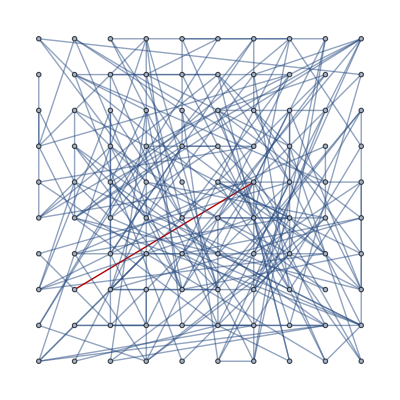
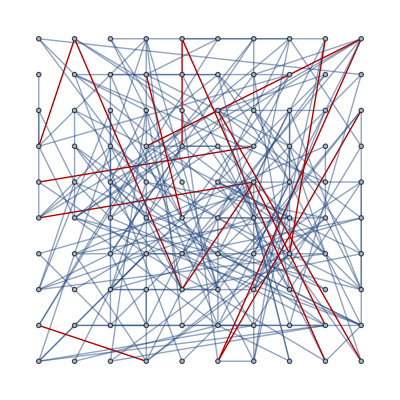
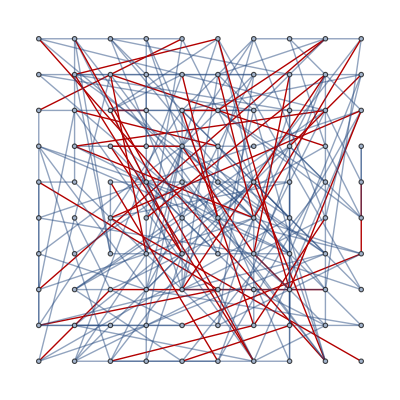
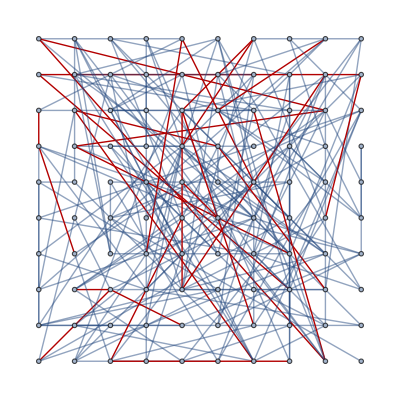
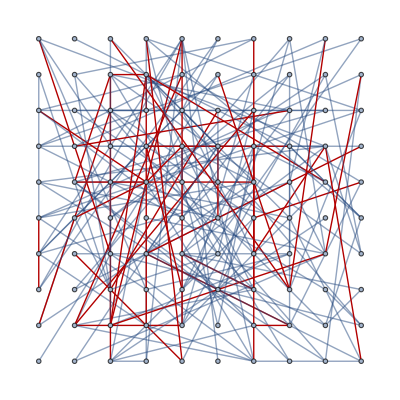
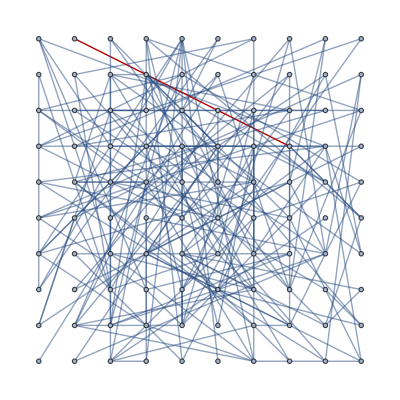
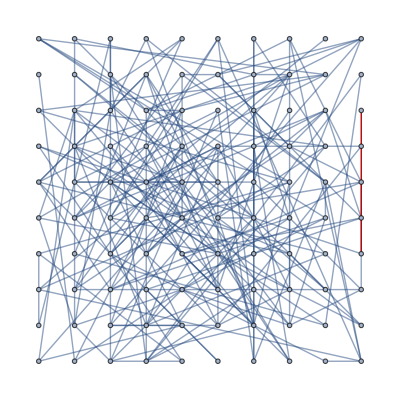
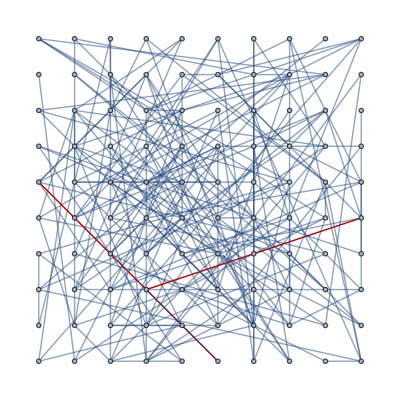
ground | Isoperimetric |  | MultipleIsoperimetric | 
-Graphics- | 101.01 | -Graphics- | 117.647 | 
-Graphics- | 176.545 | -Graphics- | 144. | 
-Graphics- | 165.657 | -Graphics- | 101.01 | 
-Graphics- | 101.01 | -Graphics- | 102.041 | 
-Graphics- | 101.01 | -Graphics- | 101.01 |

```mathematica
n=16;k=5;  (*k is the number of basis vector to use*)
spanners=(*System`RandomGraph[DegreeGraphDistribution[Table[RandomInteger[{2,3}],n]],20];*)Table[RandomGrid1[10,10, maxDist=10,maxFanOut=3], 5];
(*spanners =UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/n,n], EdgeWeight->Automatic]&/@spanners;*)

grid =Flatten[Map[(CompareIsoperimetricAlgs[#,k]&),spanners],1]; 
Grid[Prepend[grid,{"ground","Isoperimetric",Null,"MultipleIsoperimetric" , Null}], Alignment->Center, Frame->All]
(*grid = Map[OpenerView[{Grid[#[[;;1]]], Grid[#[[2;;]]]}]&, Map[(CompareIsoperimetricAlgs[#,k, ShowAll->True]&),spanners]];
Column[Prepend[grid,Grid[{{"ground","Isoperimetric",Null,"MultipleIsoperimetric" , Null}}] ]]*)
```

```mathematica
k=3;  (*k is the number of basis vector to use*)
scores=Table[
spanners=(*System`RandomGraph[DegreeGraphDistribution[Table[RandomInteger[{2,3}],n]],20];*)Table[RandomGrid1[10,10, maxDist=d,maxFanOut=f], 50];
(*spanners =UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/n,n], EdgeWeight->Automatic]&/@spanners;*)
grid =Flatten[Map[(CompareIsoperimetricAlgs[#,k]&),spanners],1]; 
With[{score=Mean[(grid[[All,2]]-grid[[All,4]])/grid[[All,2]]]},{d,f,score}],{d,{2,4,6,8,10}},{f,{1,2,3,4}}]
```

{{{2,1,0.750971},{2,2,0.50135},{2,3,0.455386},{2,4,0.424421}},{{4,1,0.72392},{4,2,0.15812},{4,3,0.179367},{4,4,0.171329}},{{6,1,0.740118},{6,2,0.219028},{6,3,0.12142},{6,4,0.0911891}},{{8,1,0.761447},{8,2,0.189317},{8,3,0.115895},{8,4,0.0726141}},{{10,1,0.764465},{10,2,0.182865},{10,3,0.0957965},{10,4,0.0897478}}}

```mathematica
scores ={{{1,1,74.75808544425804},{1,2,57.06918380332298},{1,3,56.989965456135664},{1,4,52.9935261468727},{1,5,56.68114606997931},{1,6,49.58321108420557},{1,7,45.85328316931843},{1,8,46.336731636720295}},{{2,1,80.54933283909757},{2,2,56.486652177031104},{2,3,37.95251021196501},{2,4,30.80177462119933},{2,5,30.710876534649596},{2,6,34.40422617938321},{2,7,37.54995738761638},{2,8,29.389447633776438}},{{3,1,79.97739975643155},{3,2,50.64552270549768},{3,3,2.445619898384894},{3,4,12.190375753543602},{3,5,36.59425403535},{3,6,16.17893301526611},{3,7,-23.693264465562297},{3,8,26.55592922787967}},{{4,1,71.29543982261602},{4,2,21.47306653342969},{4,3,-0.00429181791453348},{4,4,-21.917377153977117},{4,5,-11.385312691246089},{4,6,21.7492277352615},{4,7,27.17166985576479},{4,8,-39.51984225711042}},{{5,1,77.46544088989606},{5,2,14.810270310815415},{5,3,-5.97133135552303},{5,4,-12.028742814692986},{5,5,-16.068616657896012},{5,6,25.6276284871159},{5,7,-24.836378939818395},{5,8,-61.228590015605924}},{{6,1,69.25650022334554},{6,2,18.54207125488301},{6,3,-17.06433343689599},{6,4,12.311171190749578},{6,5,-21.79008076986698},{6,6,-4.9839433584717545},{6,7,17.119321105697534},{6,8,17.980080251371703}},{{7,1,73.69032630887723},{7,2,28.922840225358808},{7,3,-19.151395543373248},{7,4,6.4620105673270745},{7,5,-17.095255419299715},{7,6,6.996266925305944},{7,7,-5.269311640967754},{7,8,-21.21631488159205}},{{8,1,71.70326535673203},{8,2,14.964080660112463},{8,3,-12.245577379660007},{8,4,-49.635239916865494},{8,5,6.255329585002394},{8,6,8.95505541430188},{8,7,22.129072044620308},{8,8,25.56805847613755}},{{9,1,72.81673788070879},{9,2,7.31471964850606},{9,3,2.4054011841139062},{9,4,-26.223698828914056},{9,5,-6.299545844455906},{9,6,0.8874760408088933},{9,7,29.470555662746694},{9,8,-80.53095231523754}},{{10,1,80.43899262585977},{10,2,18.474198954171143},{10,3,5.139294927191383},{10,4,-62.289657204102255},{10,5,8.44648153594691},{10,6,5.488238559020129},{10,7,28.24669284315626},{10,8,19.658747856960918}}};
ListPointPlot3D[Flatten[scores,1]]
```

-Graphics3D-

```mathematica
img = Table[scores[[d,f,3]], {d, 1,10},{f,1,8}]
img=(img-Min[Flatten[img]])/Max[Abs[Flatten[img]]]
Image[img, ColorSpace->"Grayscale"]
```

{{74.7581,57.0692,56.99,52.9935,56.6811,49.5832,45.8533,46.3367},{80.5493,56.4867,37.9525,30.8018,30.7109,34.4042,37.55,29.3894},{79.9774,50.6455,2.44562,12.1904,36.5943,16.1789,-23.6933,26.5559},{71.2954,21.4731,-0.00429182,-21.9174,-11.3853,21.7492,27.1717,-39.5198},{77.4654,14.8103,-5.97133,-12.0287,-16.0686,25.6276,-24.8364,-61.2286},{69.2565,18.5421,-17.0643,12.3112,-21.7901,-4.98394,17.1193,17.9801},{73.6903,28.9228,-19.1514,6.46201,-17.0953,6.99627,-5.26931,-21.2163},{71.7033,14.9641,-12.2456,-49.6352,6.25533,8.95506,22.1291,25.5681},{72.8167,7.31472,2.4054,-26.2237,-6.29955,0.887476,29.4706,-80.531},{80.439,18.4742,5.13929,-62.2897,8.44648,5.48824,28.2467,19.6587}}

{{1.92787,1.70827,1.70729,1.65767,1.70345,1.61534,1.56903,1.57503},{1.99977,1.70104,1.47094,1.38217,1.38104,1.42689,1.46595,1.36463},{1.99267,1.62852,1.03013,1.15111,1.45408,1.20063,0.705626,1.32946},{1.88489,1.26635,0.999719,0.727673,0.858426,1.26978,1.3371,0.509143},{1.96149,1.18364,0.925639,0.850438,0.800284,1.31793,0.691434,0.239634},{1.85957,1.22997,0.787922,1.15261,0.729253,0.937897,1.2123,1.22299},{1.91462,1.35884,0.762012,1.08,0.787538,1.08663,0.934355,0.736377},{1.88995,1.18555,0.847746,0.383563,1.07743,1.11095,1.2745,1.31719},{1.90377,1.09058,1.02963,0.674211,0.921565,1.01079,1.36564,0.},{1.9984,1.22912,1.06357,0.226461,1.10463,1.06791,1.35045,1.24383}}

-Graphics-

```mathematica
ListPointPlot3D[Flatten[scores,1],Filling->Bottom]
```

-Graphics3D-

```mathematica
scores
```

ListPointPlot3D::arrayerr: {0.2,1.,3.60466,0.2,2.,3.78396,0.2,3.,2.85716,0.2,4.,1.75651,0.4,1.,4.17927,0.4,2.,2.40969,0.4,3.,2.69655,0.4,4.,1.46556,0.6,1.,4.02178,0.6,2.,1.82782,0.6,3.,0.286083,0.6,4.,0.897855,0.8,1.,3.7409,0.8,2.,1.0933,0.8,3.,0.88979,0.8,4.,-0.922205,1.,1.,«70»} must be a valid array or a list of valid arrays.

ListPointPlot3D[{1/5,1,3.60466,1/5,2,3.78396,1/5,3,2.85716,1/5,4,1.75651,2/5,1,4.17927,2/5,2,2.40969,2/5,3,2.69655,2/5,4,1.46556,3/5,1,4.02178,3/5,2,1.82782,3/5,3,0.286083,3/5,4,0.897855,4/5,1,3.7409,4/5,2,1.0933,4/5,3,0.88979,4/5,4,-0.922205,1,1,4.09697,1,2,0.987255,1,3,-1.1916,1,4,-2.44912,6/5,1,3.82239,6/5,2,0.325352,6/5,3,-1.76665,6/5,4,0.321487,7/5,1,3.03951,7/5,2,2.11926,7/5,3,-2.03496,7/5,4,-0.482798,8/5,1,3.8821,8/5,2,1.6748,8/5,3,-0.142489,8/5,4,-1.0808,9/5,1,3.59242,9/5,2,0.348526,9/5,3,0.38048,9/5,4,0.334143,2,1,3.6503,2,2,1.66255,2,3,-0.256551,2,4,0.504272},Filling→Bottom]

```mathematica
ListPointPlot3D[scores,Filling->Bottom]
```

-Graphics3D-

-Graphics3D-

```mathematica
Column[Map[OpenerView[{Grid[#], Grid[#*2]}]&, {{{1,2,3}},{{4,5,6}},{{7,8,9}}}]]
```

```mathematica
{5,2,7,4}[[5;;]]
```

{}

```mathematica
RandomInteger[{1,10},100]
```

{3,6,3,4,10,7,1,3,8,9,7,6,7,3,10,8,1,2,2,6,6,5,10,3,3,9,6,6,6,5,5,3,7,3,2,7,3,8,8,4,10,2,1,6,5,7,8,6,1,1,2,4,10,2,2,9,1,1,10,7,7,10,5,4,9,10,8,10,8,2,7,1,3,6,8,2,7,9,10,8,4,5,8,10,5,5,2,6,5,9,9,3,4,9,8,1,1,10,5,8}

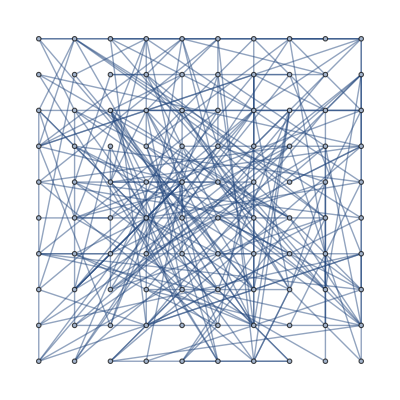

grounds:{27,47,82,74,35}

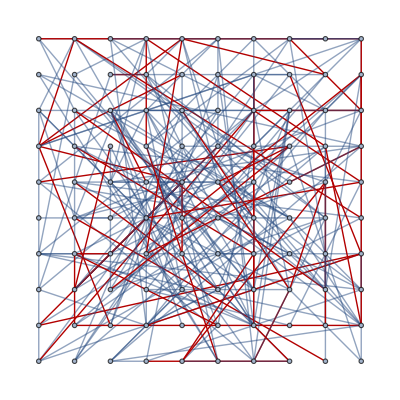
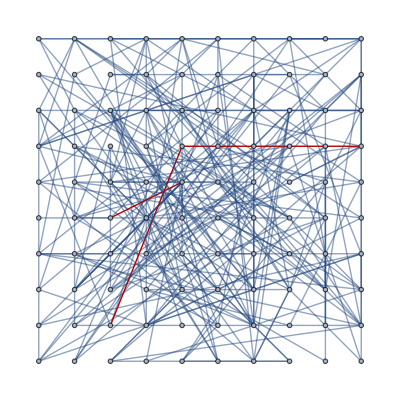
{{-Graphics-,219.156,-Graphics-,103.093}}

```mathematica
g=spanners[[1]]
CompareIsoperimetricAlgs[g,5]
```

```mathematica
comp=#[[1]]&/@ConnectedComponents[EdgeList[g]]
```

{32,20,1}

```mathematica
comp[[Mod[1,5]+1]]
```

20

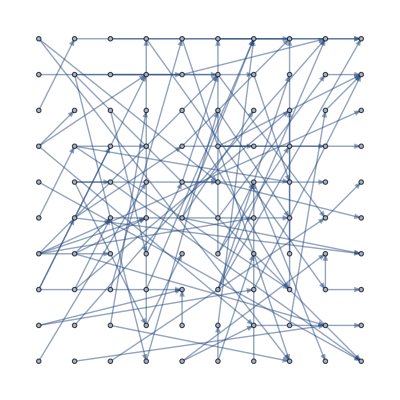
AddEdges[{1<->2},-Graphics-]

```mathematica
AddEdges[{1<->2},g]
```

```mathematica
Range[5]
```

{1,2,3,4,5}

Circle

```mathematica
Map[UndirectedEdge[comp[[1]], #]&,comp[[2;;]]]
```

{32<->20,32<->1}

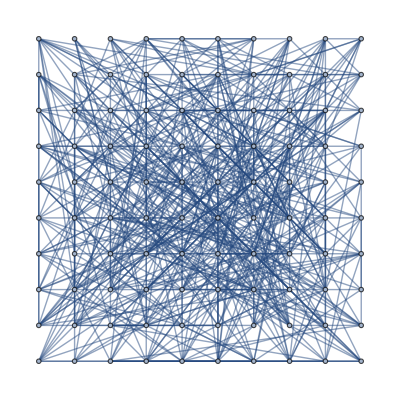

```mathematica
RandomGrid1[10,10, maxDist=10,maxFanOut=5]
```

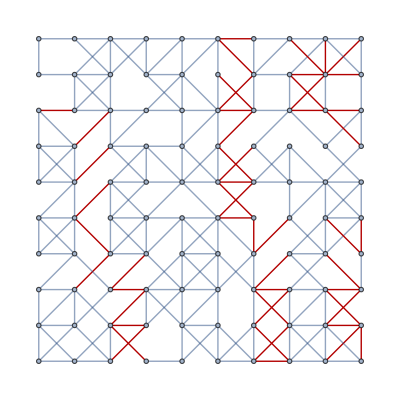

```mathematica
ShowIsoperimetricCut[RandomGrid1[10,10]]
```